# Ve401 Midterm RC

## Mathematica Part

Based on Zhang Fan’s Mathematica Summary

## Elements of Probability Theory

### Permutation and Combination

Permutation of k objects from A (total n elements)

```mathematica
Binomial[n,k]*k!
```

```mathematica
Binomial[7,3]*3!
```

210

Combination of k objects from A (total n elements)

```mathematica
Binomial[n,k]
```

```mathematica
Binomial[7,3]
```

35

### PDF and CDF

Basic Idea:

```mathematica
PDFSomeDistribution[Parameters],value;
CDFSomeDistribution[Parameters],value;
InverseCDFSomeDistribution[Parameters],probability;
MeanSomeDistribution[Parameters];
VarianceSomeDistributionPariance;
MomentGeneratingFunctionSomeDistribution[Parameters],variablevalue;
```

Example

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
InverseCDF[NormalDistribution[μ,σ],0.975]
```

μ+1.95996 σ

```mathematica
Mean[NormalDistribution[μ,σ]]
```

μ

```mathematica
Variance[NormalDistribution[μ,σ]]
```

σ^2

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],t]
```

ⅇ^(t μ+(t^2 σ^2)/2)

For every distribution mentioned in the slide, Mathematica should have a corresponding Distribution. But be careful, distribution in Mathematica may be defined differently from the slide! (Especially when it  comes to gamma function Γ)

### Transformation of Variables

```mathematica
X=SomeDistribution[Parameters];
Y=SomeDistribution[Parameters];

Z=TransformedDistribution[Z(X,Y),{x\[Distributed]X,y\[Distributed]Y}];
Z
```

```mathematica
X=NormalDistribution[0,1];
Y=NormalDistribution[0,1];
(*Define the new variable Z=X^2+Y^2*)
Z=TransformedDistribution[x^2+y^2,{x\[Distributed]X,y\[Distributed]Y}];
(*Display the distribution of Z*)
Z
```

ChiSquareDistribution[2]

## Introduction to Statistics

```mathematica
data:={79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29};
```

### Samples and Data - Basic Quantities

Quartiles

```mathematica
Quartiles[data]
```

{35,87,299/2}

Interquartile Range

```mathematica
InterquartileRange[data]
```

229/2

### Histogram

Freedman-Diaconis Bin Width

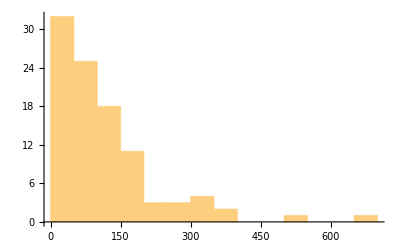

-Graphics-

```mathematica
Histogram[data,"FreedmanDiaconis"]
Histogram[data,{"Raw","FreedmanDiaconis"}]
```

Sturges’s Rule Bin Number

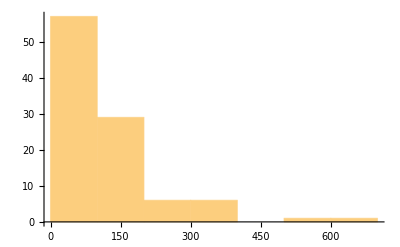

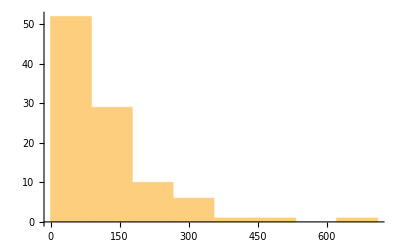

```mathematica
Histogram[data,"Sturges"]
Histogram[data,{"Raw","Sturges"}]
```

### Parameter Estimation

```mathematica
FindDistributionParameters[data,ExponentialDistribution[β],ParameterEstimator->"MethodOfMoments"]
```

{β→0.0087382}

```mathematica
FindDistributionParameters[data,ExponentialDistribution[β],ParameterEstimator->"MaximumLikelihood"]
```

{β→0.0087382}

### Interval Estimation

```mathematica
Data:={5.8,6.0,7.8,7.4,6.2,6.1,8.6,9.7,4.4,4.4,7.6,9.0,9.2,6.4,7.0,8.7,6.0,6.1,6.8,10.,5.3,8.1,8.9,5.3,6.7,5.6,3.7,8.7,6.6,10.1,6.9,6.6,6.4,5.1};
```

z_(α/2)

```mathematica
InverseCDF[NormalDistribution[],1-α/2]
```

ϰ_(α/2)^2

```mathematica
InverseCDF[ChiSquareDistribution[n],1-α/2]
```

t_(α/2)

```mathematica
InverseCDF[StudentTDistribution[n],1-α/2]
```

Length, Sample Mean and Sample Variance of Data

```mathematica
Length[Data]
Mean[Data]
Variance[Data](*It's unbiased estimate. Not population variance!*)
```

34

6.97647

2.77822

### Example: compute the two-sided 95% confidence interval for the mean

Direct Computation:

```mathematica
n=Length[Data];
α=.05;
mean=Mean[Data];
s=Sqrt[ Variance[Data]];
t=InverseCDF[StudentTDistribution[n-1],1-α/2];
L=t*s /√n;
mean-L
mean+L
```

6.3949

7.55804

MeanCI :

```mathematica
Needs["HypothesisTesting`"]
MeanCI[Data,ConfidenceLevel->.95]
VarianceCI[Data,ConfidenceLevel->.90]
```

{6.3949,7.55804}

{1.93421,4.39369}